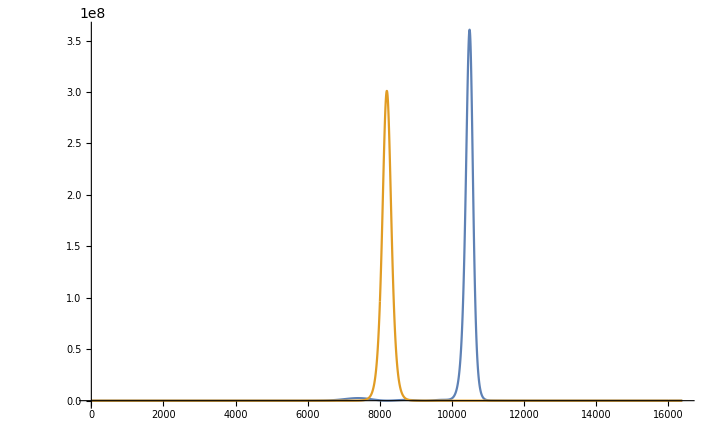

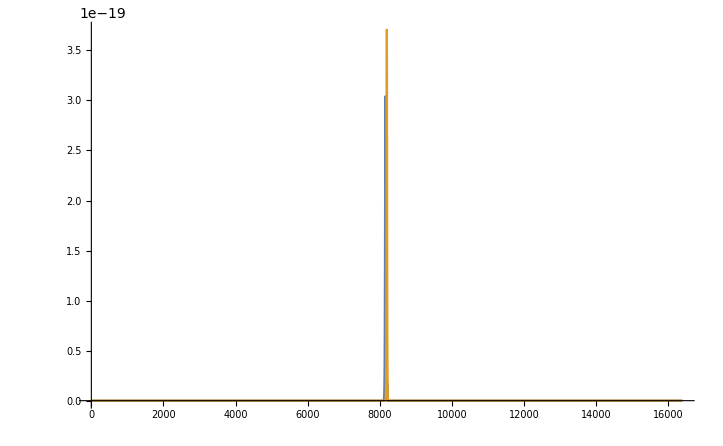

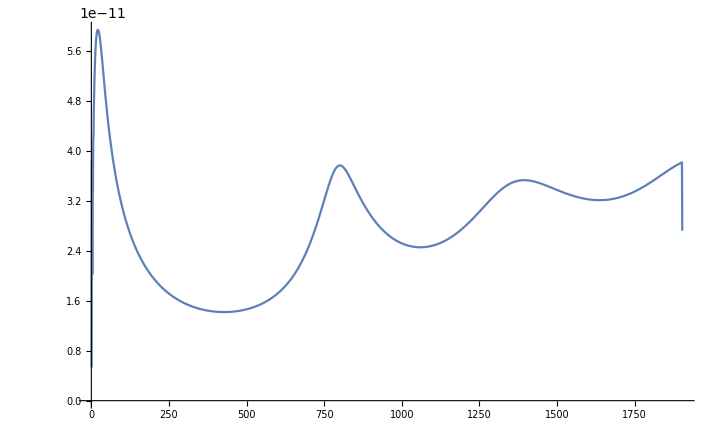

-Graphics3D-

-Graphics3D-

```mathematica
dir = "/home/s_koval/Code/julia/fl/out";
getCplxData[fname_,dir_]:=Module[{dataRaw},
dataRaw=Import[FileNameJoin[{dir,fname}],"TSV"];
ToExpression[StringReplace[#,{"im"->"*I","e"->"*10^"}]&/@dataRaw]]

u0=Flatten@getCplxData["u0.tsv",dir];
u1=Flatten@getCplxData["u1.tsv",dir];
u0w=Flatten@getCplxData["U0.tsv",dir];
u1w=Flatten@getCplxData["U1.tsv",dir];
u=Abs/@getCplxData["u_plot.tsv",dir];
uw=Abs/@getCplxData["U_plot.tsv",dir];

steps=Import["/home/s_koval/Code/julia/fl/out/steps.tsv","TSV"];
s=Flatten[steps];

ListPlot[{Abs[u1]^2, Abs[u0]^2},Joined->True,PlotRange->Full]
ListPlot[{Abs[u1w]^2, Abs[u0w]^2},Joined->True,PlotRange->Full]
ListPlot[s, Joined->True, PlotRange->Full]
ListPlot3D[u, PlotRange->Full]
ListPlot3D[uw, PlotRange->Full]
```